## Initial data

### Epsilons

A selection of epsilons for plotting .

```mathematica
ϵs={0.1,0.5,1,2,10}
```

{0.1,0.5,1,2,10}

### Poly-harmonic k-values

A selection of k-values for plotting poly-harmonic splines .

```mathematica
ks={0,1,2,3,4,5}
```

{0,1,2,3,4,5}

### Sample r-values

A set of points at which to evaluate RBFs

```mathematica
rs=Range[-1,1,0.2]
```

{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

## Glossary of RBFs

### Gaussian

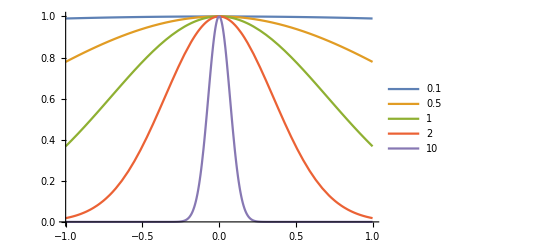

{0.99005,0.99362,0.996406,0.998401,0.9996,1.,0.9996,0.998401,0.996406,0.99362,0.99005}

{0.367879,0.527292,0.697676,0.852144,0.960789,1.,0.960789,0.852144,0.697676,0.527292,0.367879}

```mathematica
Gaussian[ϵ_]=Function[r,Exp[-(ϵ Abs[r])^2]];
Show[
Plot[Evaluate@Table[Gaussian[ϵ][r],{ϵ,ϵs}],{r,-1,1},PlotLegends->ϵs],
AxesOrigin->{-1,0}
]
Table[Gaussian[0.1][r],{r,rs}]
Table[Gaussian[1][r],{r,rs}]
```

### Multi-quadric

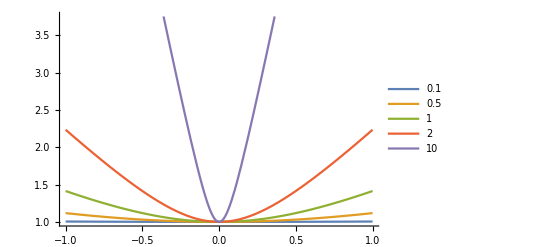

{1.00499,1.00319,1.0018,1.0008,1.0002,1.,1.0002,1.0008,1.0018,1.00319,1.00499}

{1.41421,1.28062,1.16619,1.07703,1.0198,1.,1.0198,1.07703,1.16619,1.28062,1.41421}

```mathematica
Multiquadric[ϵ_]=Function[r,√(1+(ϵ Abs[r])^2)];
Show[
Plot[Evaluate@Table[Multiquadric[ϵ][r],{ϵ,ϵs}],{r,-1,1},PlotLegends->ϵs],
AxesOrigin->{-1,0}
]
Table[Multiquadric[0.1][r],{r,rs}]
Table[Multiquadric[1][r],{r,rs}]
```

### Inverse multi-quadric

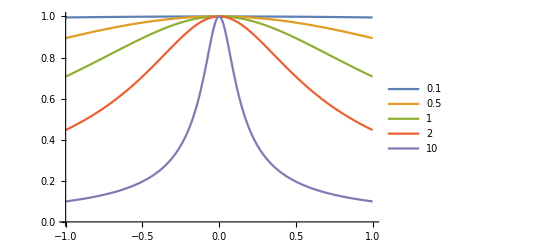

{0.995037,0.996815,0.998205,0.999201,0.9998,1.,0.9998,0.999201,0.998205,0.996815,0.995037}

{0.707107,0.780869,0.857493,0.928477,0.980581,1.,0.980581,0.928477,0.857493,0.780869,0.707107}

```mathematica
InverseMultiquadric[ϵ_]=Function[r,1/(√(1+(ϵ Abs[r])^2))];
Show[
Plot[Evaluate@Table[InverseMultiquadric[ϵ][r],{ϵ,ϵs}],{r,-1,1},PlotLegends->ϵs],
AxesOrigin->{-1,0}
]
Table[InverseMultiquadric[0.1][r],{r,rs}]
Table[InverseMultiquadric[1][r],{r,rs}]
```

### Inverse quadric

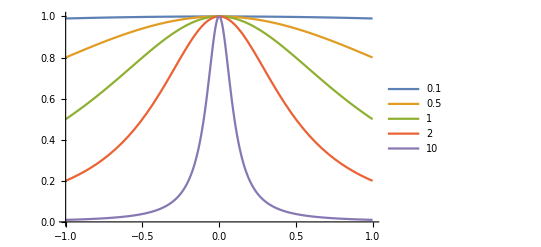

{0.990099,0.993641,0.996413,0.998403,0.9996,1.,0.9996,0.998403,0.996413,0.993641,0.990099}

{0.5,0.609756,0.735294,0.862069,0.961538,1.,0.961538,0.862069,0.735294,0.609756,0.5}

```mathematica
InverseQuadric[ϵ_]=Function[r,1/(1+(ϵ Abs[r])^2)];
Show[
Plot[Evaluate@Table[InverseQuadric[ϵ][r],{ϵ,ϵs}],{r,-1,1},PlotLegends->ϵs],
AxesOrigin->{-1,0}
]
Table[InverseQuadric[0.1][r],{r,rs}]
Table[InverseQuadric[1][r],{r,rs}]
```

### Poly-harmonic spline

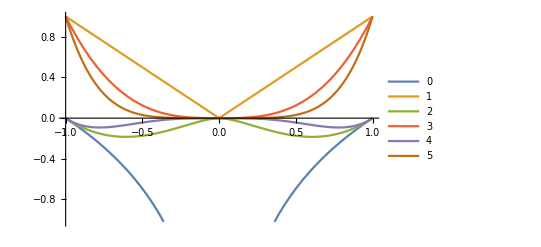

{0.,-0.142812,-0.183897,-0.146607,-0.0643775,0,-0.0643775,-0.146607,-0.183897,-0.142812,0.}

{1.,0.512,0.216,0.064,0.008,0.,0.008,0.064,0.216,0.512,1.}

```mathematica
PolyharmonicSpline[k_]=If[Mod[k,2]==0,Function[r,If[Abs[r]>0,Abs[r]^k Log[Abs[r]],0]],Function[r,Abs[r]^k]];
Show[
Plot[Evaluate@Table[PolyharmonicSpline[k][r],{k,ks}],{r,-1,1},PlotLegends->ks],
AxesOrigin->{-1,0}
]
Table[PolyharmonicSpline[2][r],{r,rs}]
Table[PolyharmonicSpline[3][r],{r,rs}]
```

### Bump

General::munfl: Exp[-12238.] is too small to represent as a normalized machine number; precision may be lost.

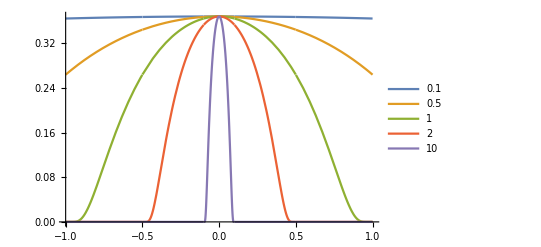

{0.364182,0.365517,0.366553,0.36729,0.367732,0.367879,0.367732,0.36729,0.366553,0.365517,0.364182}

{0,0.0621765,0.209611,0.304076,0.352866,0.367879,0.352866,0.304076,0.209611,0.0621765,0}

```mathematica
Bump[ϵ_]=Function[r,If[Abs[r]<1/ϵ,Exp[-1/(1-(ϵ Abs[r])^2)],0]];
Show[
Plot[Evaluate@Table[Bump[ϵ][r],{ϵ,ϵs}],{r,-1,1},PlotLegends->ϵs],
AxesOrigin->{-1,0}
]
Table[Bump[0.1][r],{r,rs}]
Table[Bump[1][r],{r,rs}]
```

## Verification

### Data setup

```mathematica
ps={{0.5,0.5,0.5},{0.75,0.75,0.75}};
v={0,1};

d[u_,v_]:=√((u[[1]]-v[[1]])^2+(u[[2]]-v[[2]])^2+(u[[3]]-v[[3]])^2);
```

### Gaussian

```mathematica
Module[{ϕ,M,w,ψ},
ϕ=Gaussian[2];

M=({{ϕ[d[ps[[1]],ps[[1]]]], ϕ[d[ps[[1]],ps[[2]]]]}, {ϕ[d[ps[[2]],ps[[1]]]], ϕ[d[ps[[2]],ps[[2]]]]}});

w=LinearSolve[M,v];

ψ=Function[{x,y,z},w[[1]]*ϕ[d[ps[[1]],{x,y,z}]]+w[[2]]*ϕ[d[ps[[2]],{x,y,z}]]];

Print[ψ[0.5,0.5,0.5]];
Print[ψ[0.625,0.625,0.625]];
Print[ψ[0.75,0.75,0.75]];
]
```

0.

0.563059

1.

### Multi-quadric

```mathematica
Module[{ϕ,M,w,ψ},
ϕ=Multiquadric[2];

M=({{ϕ[d[ps[[1]],ps[[1]]]], ϕ[d[ps[[1]],ps[[2]]]]}, {ϕ[d[ps[[2]],ps[[1]]]], ϕ[d[ps[[2]],ps[[2]]]]}});

w=LinearSolve[M,v];

ψ=Function[{x,y,z},w[[1]]*ϕ[d[ps[[1]],{x,y,z}]]+w[[2]]*ϕ[d[ps[[2]],{x,y,z}]]];

Print[ψ[0.5,0.5,0.5]];
Print[ψ[0.625,0.625,0.625]];
Print[ψ[0.75,0.75,0.75]];
]
```

0.

0.469127

1.

### Inverse multi-quadric

```mathematica
Module[{ϕ,M,w,ψ},
ϕ=InverseMultiquadric[2];

M=({{ϕ[d[ps[[1]],ps[[1]]]], ϕ[d[ps[[1]],ps[[2]]]]}, {ϕ[d[ps[[2]],ps[[1]]]], ϕ[d[ps[[2]],ps[[2]]]]}});

w=LinearSolve[M,v];

ψ=Function[{x,y,z},w[[1]]*ϕ[d[ps[[1]],{x,y,z}]]+w[[2]]*ϕ[d[ps[[2]],{x,y,z}]]];

Print[ψ[0.5,0.5,0.5]];
Print[ψ[0.625,0.625,0.625]];
Print[ψ[0.75,0.75,0.75]];
]
```

0.

0.522608

1.

### Inverse quadric

```mathematica
Module[{ϕ,M,w,ψ},
ϕ=InverseQuadric[2];

M=({{ϕ[d[ps[[1]],ps[[1]]]], ϕ[d[ps[[1]],ps[[2]]]]}, {ϕ[d[ps[[2]],ps[[1]]]], ϕ[d[ps[[2]],ps[[2]]]]}});

w=LinearSolve[M,v];

ψ=Function[{x,y,z},w[[1]]*ϕ[d[ps[[1]],{x,y,z}]]+w[[2]]*ϕ[d[ps[[2]],{x,y,z}]]];

Print[ψ[0.5,0.5,0.5]];
Print[ψ[0.625,0.625,0.625]];
Print[ψ[0.75,0.75,0.75]];
]
```

0.

0.535885

1.

### PolyharmonicSpline

```mathematica
Module[{ϕ,M,w,ψ},
ϕ=PolyharmonicSpline[2];

M=({{ϕ[d[ps[[1]],ps[[1]]]], ϕ[d[ps[[1]],ps[[2]]]]}, {ϕ[d[ps[[2]],ps[[1]]]], ϕ[d[ps[[2]],ps[[2]]]]}});

w=LinearSolve[M,v];

ψ=Function[{x,y,z},w[[1]]*ϕ[d[ps[[1]],{x,y,z}]]+w[[2]]*ϕ[d[ps[[2]],{x,y,z}]]];

Print[ψ[0.5,0.5,0.5]];
Print[ψ[0.625,0.625,0.625]];
Print[ψ[0.75,0.75,0.75]];
]
```

0.

0.457036

1.

### Bump

```mathematica
Module[{ϕ,M,w,ψ},
ϕ=Bump[0.1];

M=({{ϕ[d[ps[[1]],ps[[1]]]], ϕ[d[ps[[1]],ps[[2]]]]}, {ϕ[d[ps[[2]],ps[[1]]]], ϕ[d[ps[[2]],ps[[2]]]]}});

w=LinearSolve[M,v];

ψ=Function[{x,y,z},w[[1]]*ϕ[d[ps[[1]],{x,y,z}]]+w[[2]]*ϕ[d[ps[[2]],{x,y,z}]]];

Print[ψ[0.5,0.5,0.5]];
Print[ψ[0.625,0.625,0.625]];
Print[ψ[0.75,0.75,0.75]];
]
```

0.

0.500235

1.